```mathematica
ClearSystemCache[];
ClearAll["Global`*"]
```

### Task & Variables

Find distribution of electrical field in a condensator consisting of two flat plates located in one plane. Length of each plate is 3mm, distance between plates is 3mm, their potentials are 0V and +30V. Solve the task in 2D

```mathematica
l = 3×10^-3;
d = 3×10^-3;
t =10^-5; (*thickness of plates*)
φ1 = 0.0;
φ2 = 30.0;
stepX = 3×10^-4;
stepY = t;
Nx =N[ l/stepX];
Ny = N[t/stepY];
Nb = 2Nx+2Ny; (*size of boundary arrays*)
```

### Calculation

#### Setting up boundaries

```mathematica
Plate = Table[0.0,{i,Nb},{j,4}];
PlateKnots=Table[0.0,{i,Nb},{j,2}];
For[i =1,i≤Nx,i++,Plate[[i,1]]=stepX×(i-1);Plate[[i,2]]=0.0;Plate[[i,3]]=stepX×i;Plate[[i,4]]=0.0];
For[i =1,i≤Ny,i++,Plate[[i+Nx,1]]=l;Plate[[i+Nx,2]]=stepY×(i-1);Plate[[i+Nx,3]]=l;Plate[[i+Nx,4]]=stepY×i];
For[i =1,i≤Nx,i++,Plate[[i+Nx+Ny,1]]=l-stepX×(i-1);Plate[[i+Nx+Ny,2]]=t;Plate[[i+Nx+Ny,3]]=l-stepX×i;
Plate[[i+Nx+Ny,4]]=t];
For[i =1,i≤Ny,i++,Plate[[i+2Nx+Ny,1]]=0.0;Plate[[i+2Nx+Ny,2]]=t-stepY×(i-1);Plate[[i+2Nx+Ny,3]]=0.0;
Plate[[i+2Nx+Ny,4]]=t-stepY×i];
For[i=1,i≤Nb,i++,PlateKnots[[i,1]]=(Plate[[i,1]]+Plate[[i,3]])/2;PlateKnots[[i,2]]=(Plate[[i,2]]+Plate[[i,4]])/2];
```

```mathematica
LeftPlate = Plate;
RightPlate = Plate;
LeftPlateKnots = PlateKnots;
RightPlateKnots = PlateKnots;
RightPlate[[All,1]]=RightPlate[[All,1]]+d+l;
RightPlate[[All,3]]=RightPlate[[All,3]]+d+l;
RightPlateKnots[[All,1]]=RightPlateKnots[[All,1]]+d+l;
```

```mathematica
Boundary = Join[LeftPlate,RightPlate];
BoundaryKnots= Join[LeftPlateKnots,RightPlateKnots];
```

```mathematica
N[Boundary]//MatrixForm
```

(0. | 0. | 0.0003 | 0.
0.0003 | 0. | 0.0006 | 0.
0.0006 | 0. | 0.0009 | 0.
0.0009 | 0. | 0.0012 | 0.
0.0012 | 0. | 0.0015 | 0.
0.0015 | 0. | 0.0018 | 0.
0.0018 | 0. | 0.0021 | 0.
0.0021 | 0. | 0.0024 | 0.
0.0024 | 0. | 0.0027 | 0.
0.0027 | 0. | 0.003 | 0.
0.003 | 0. | 0.003 | 0.00001
0.003 | 0.00001 | 0.0027 | 0.00001
0.0027 | 0.00001 | 0.0024 | 0.00001
0.0024 | 0.00001 | 0.0021 | 0.00001
0.0021 | 0.00001 | 0.0018 | 0.00001
0.0018 | 0.00001 | 0.0015 | 0.00001
0.0015 | 0.00001 | 0.0012 | 0.00001
0.0012 | 0.00001 | 0.0009 | 0.00001
0.0009 | 0.00001 | 0.0006 | 0.00001
0.0006 | 0.00001 | 0.0003 | 0.00001
0.0003 | 0.00001 | 0. | 0.00001
0. | 0.00001 | 0. | 0.
0.006 | 0. | 0.0063 | 0.
0.0063 | 0. | 0.0066 | 0.
0.0066 | 0. | 0.0069 | 0.
0.0069 | 0. | 0.0072 | 0.
0.0072 | 0. | 0.0075 | 0.
0.0075 | 0. | 0.0078 | 0.
0.0078 | 0. | 0.0081 | 0.
0.0081 | 0. | 0.0084 | 0.
0.0084 | 0. | 0.0087 | 0.
0.0087 | 0. | 0.009 | 0.
0.009 | 0. | 0.009 | 0.00001
0.009 | 0.00001 | 0.0087 | 0.00001
0.0087 | 0.00001 | 0.0084 | 0.00001
0.0084 | 0.00001 | 0.0081 | 0.00001
0.0081 | 0.00001 | 0.0078 | 0.00001
0.0078 | 0.00001 | 0.0075 | 0.00001
0.0075 | 0.00001 | 0.0072 | 0.00001
0.0072 | 0.00001 | 0.0069 | 0.00001
0.0069 | 0.00001 | 0.0066 | 0.00001
0.0066 | 0.00001 | 0.0063 | 0.00001
0.0063 | 0.00001 | 0.006 | 0.00001
0.006 | 0.00001 | 0.006 | 0.)

#### Influence matrices

```mathematica
ρ[x_,y_,x0_,y0_]:=√((x-x0)^2+(y-y0)^2);
w[x_,y_,x0_,y0_]:=N[1/(2π)×Log[ρ[x,y,x0,y0]]]; (*Green's function*)
wx[x_,y_,x0_,y0_]:=N[1/(2π)1/ρ[x,y,x0,y0]^2(x-x0)];
wy[x_,y_,x0_,y0_]:=N[1/(2π)1/ρ[x,y,x0,y0]^2(y-y0)];
```

```mathematica
G(*[x1_,y1_,x2_,y2_,x0_,y0_]:=G[x1,y1,x2,y2,x0,y0]*)=Compile[{x1,y1,x2,y2,x0,y0},Block[{L,tabX,tabY,tabW,n,res},L=Norm[{x2-x1,y2-y1}];n=101.0;tabX=Table[x1+(i-1)×(x2-x1)/n,{i,n+1}];tabY=Table[y1+(i-1)×(y2-y1)/n,{i,n+1}];tabW=Table[w[tabX[[i]],tabY[[i]],x0,y0],{i,n+1}];res=(1.-0.)/(2n)×Sum[tabW[[i]]+tabW[[i+1]],{i,1,n}]×L;res]];
H(*[x1_,y1_,x2_,y2_,x0_,y0_]:=H[x1,y1,x2,y2,x0,y0]*)=Compile[{x1,y1,x2,y2,x0,y0},Block[{L,tabX,tabY,tabW,n,n1,n2,res},L=Norm[{x2-x1,y2-y1}];n=101.0;tabX=Table[x1+(i-1)×(x2-x1)/n,{i,n+1}];tabY=Table[y1+(i-1)×(y2-y1)/n,{i,n+1}];n1=(y2-y1)/L;n2=(x1-x2)/L;
tabDW=Table[wx[tabX[[i]],tabY[[i]],x0,y0]×n1+wy[tabX[[i]],tabY[[i]],x0,y0]×n2,{i,n+1}];res=(1.-0.)/(2n)×Sum[tabDW[[i]]+tabDW[[i+1]],{i,1,n}]×L;res]];
```

```mathematica
Gm=ParallelTable[N[G[Boundary[[j,1]],Boundary[[j,2]],Boundary[[j,3]],Boundary[[j,4]],BoundaryKnots[[i,1]],BoundaryKnots[[i,2]]]],{i,2Nb},{j,2Nb}];
```

```mathematica
Hm=ParallelTable[N[H[Boundary[[j,1]],Boundary[[j,2]],Boundary[[j,3]],Boundary[[j,4]],BoundaryKnots[[i,1]],BoundaryKnots[[i,2]]]],{i,2Nb},{j,2Nb}];
```

#### Solving BEM main equation in matrix form

G_ij q_j=(H_ij+1/2 E)u_j

```mathematica
u1=Table[φ1,{i,Nb}];
u2=Table[φ2,{i,Nb}];
u=Join[u1,u2];
q=Inverse[Gm].(Hm+0.5×IdentityMatrix[IntegerPart[2Nb]]).u;
```

```mathematica
gridBoundLeft = -l;
gridBoundRight = 4l;
gridBoundDown= -l;
gridBoundUp = l;
NxGrid=29.0;
NyGrid=29.0;
xGrid=ParallelTable[gridBoundLeft+(i-1)×(gridBoundRight-gridBoundLeft)/NxGrid,{i,NxGrid+1}];
yGrid=ParallelTable[gridBoundDown+(i-1)×(gridBoundUp-gridBoundDown)/NyGrid,{i,NyGrid+1}];
N[xGrid]
N[yGrid]
```

{-0.003,-0.00248276,-0.00196552,-0.00144828,-0.000931034,-0.000413793,0.000103448,0.00062069,0.00113793,0.00165517,0.00217241,0.00268966,0.0032069,0.00372414,0.00424138,0.00475862,0.00527586,0.0057931,0.00631034,0.00682759,0.00734483,0.00786207,0.00837931,0.00889655,0.00941379,0.00993103,0.0104483,0.0109655,0.0114828,0.012}

{-0.003,-0.0027931,-0.00258621,-0.00237931,-0.00217241,-0.00196552,-0.00175862,-0.00155172,-0.00134483,-0.00113793,-0.000931034,-0.000724138,-0.000517241,-0.000310345,-0.000103448,0.000103448,0.000310345,0.000517241,0.000724138,0.000931034,0.00113793,0.00134483,0.00155172,0.00175862,0.00196552,0.00217241,0.00237931,0.00258621,0.0027931,0.003}

WARNING: this little maneuver is gonna cost us ~10 minutes

```mathematica
phi=Table[0.0,{i,NxGrid+1},{j,NyGrid+1}];
For[i=1,i≤NxGrid+1,i++,
For[j=1,j≤NyGrid+1,j++,If[xGrid[[j]]>0 &&xGrid[[j]]<l &&yGrid[[i]]>0 &&yGrid[[i]]<t,InsideLeft=True, If[xGrid[[j]]>l+d &&xGrid[[j]]<d+2l &&yGrid[[i]]>0 &&yGrid[[i]]<t,InsideRight=True,InsideLeft=False;InsideRight=False]];If[InsideLeft==True,phi[[i,j]]=φ1,If[InsideRight==True,phi[[i,j]]=φ2,For[k=1,k≤2Nb,k++,phi[[i,j]]=phi[[i,j]]+q[[k]]×G[Boundary[[k,1]],Boundary[[k,2]],Boundary[[k,3]],Boundary[[k,4]],xGrid[[j]],yGrid[[i]]]-u[[k]]×H[Boundary[[k,1]],Boundary[[k,2]],Boundary[[k,3]],Boundary[[k,4]],xGrid[[j]],yGrid[[i]]]]]]]]
```

### Solution

#### Potential distribution matrix

```mathematica
phi//MatrixForm
```

(7.02524 | 6.94763 | 6.87529 | 6.81856 | 6.79309 | 6.82032 | 6.92626 | 7.13855 | 7.48265 | 7.97871 | 8.63882 | 9.46348 | 10.438 | 11.5316 | 12.7003 | 13.8918 | 15.0502 | 16.119 | 17.0475 | 17.7969 | 18.3457 | 18.6894 | 18.838 | 18.8132 | 18.6463 | 18.3743 | 18.0343 | 17.6577 | 17.2677 | 16.8797
6.94266 | 6.84671 | 6.75198 | 6.66877 | 6.6136 | 6.61015 | 6.68814 | 6.87951 | 7.21383 | 7.71491 | 8.3981 | 9.26615 | 10.3041 | 11.4777 | 12.7372 | 14.0244 | 15.2766 | 16.4304 | 17.4274 | 18.224 | 18.7968 | 19.1428 | 19.2744 | 19.2167 | 19.0061 | 18.6856 | 18.2979 | 17.8783 | 17.4516 | 17.0332
6.86085 | 6.74565 | 6.62693 | 6.51462 | 6.42593 | 6.387 | 6.43184 | 6.59751 | 6.91821 | 7.42179 | 8.12753 | 9.04132 | 10.1483 | 11.4099 | 12.7697 | 14.1626 | 15.5189 | 16.767 | 17.8398 | 18.6871 | 19.2845 | 19.6308 | 19.7413 | 19.6449 | 19.3834 | 19.0074 | 18.5665 | 18.0999 | 17.634 | 17.184
6.78046 | 6.64524 | 6.50096 | 6.35682 | 6.23042 | 6.15049 | 6.15615 | 6.29059 | 6.59321 | 7.09612 | 7.82334 | 8.78518 | 9.96746 | 11.3263 | 12.7969 | 14.3065 | 15.7786 | 17.132 | 18.2886 | 19.1906 | 19.8126 | 20.1566 | 20.2415 | 20.0996 | 19.7791 | 19.3395 | 18.8389 | 18.3212 | 17.8138 | 17.3309
6.7022 | 6.54635 | 6.3751 | 6.19637 | 6.02766 | 5.90036 | 5.85977 | 5.95665 | 6.23605 | 6.73436 | 7.48121 | 8.49328 | 9.75803 | 11.2247 | 12.8178 | 14.4564 | 16.0572 | 17.5288 | 18.7787 | 19.7394 | 20.3855 | 20.7241 | 20.7782 | 20.5831 | 20.1937 | 19.6812 | 19.1138 | 18.5406 | 17.9895 | 17.4729
6.62685 | 6.45001 | 6.25059 | 6.03455 | 5.81851 | 5.63644 | 5.5413 | 5.59336 | 5.84378 | 6.33267 | 7.09618 | 8.1603 | 9.51588 | 11.1028 | 12.8314 | 14.6121 | 16.3565 | 17.9615 | 19.3158 | 20.339 | 21.0077 | 21.3373 | 21.3551 | 21.098 | 20.628 | 20.0312 | 19.3892 | 18.7563 | 18.1597 | 17.6087
6.55525 | 6.35735 | 6.12889 | 5.873 | 5.60425 | 5.35875 | 5.19908 | 5.19813 | 5.41332 | 5.88693 | 6.66251 | 7.77978 | 9.23623 | 10.9584 | 12.8368 | 14.7734 | 16.6778 | 18.4348 | 19.9069 | 20.996 | 21.6843 | 22.0005 | 21.9764 | 21.6474 | 21.0826 | 20.388 | 19.6627 | 18.966 | 18.3223 | 17.737
6.4883 | 6.26966 | 6.01175 | 5.71384 | 5.38674 | 5.06752 | 4.83115 | 4.76804 | 4.9416 | 5.39291 | 6.1735 | 7.3437 | 8.91347 | 10.7894 | 12.8329 | 14.9393 | 17.0222 | 18.9544 | 20.5608 | 21.7177 | 22.4204 | 22.7181 | 22.647 | 22.2352 | 21.5577 | 20.7491 | 19.9311 | 19.1669 | 18.4756 | 17.8564
6.42692 | 6.18829 | 5.90116 | 5.55976 | 5.16863 | 4.76337 | 4.43491 | 4.29967 | 4.42569 | 4.84649 | 5.62143 | 6.84172 | 8.54099 | 10.5943 | 12.8195 | 15.1083 | 17.3896 | 19.527 | 21.2889 | 22.513 | 23.2209 | 23.4945 | 23.3731 | 22.8668 | 22.0535 | 21.1105 | 20.1902 | 19.3558 | 18.6171 | 17.9654
6.37205 | 6.1147 | 5.7994 | 5.41408 | 4.95376 | 4.44755 | 4.00666 | 3.78889 | 3.86316 | 4.24411 | 4.99739 | 6.25992 | 8.11097 | 10.3734 | 12.7965 | 15.2773 | 17.7779 | 20.1608 | 22.1066 | 23.3915 | 24.0899 | 24.3334 | 24.1617 | 23.5497 | 22.5692 | 21.4667 | 20.4348 | 19.5292 | 18.7447 | 18.0625
6.32458 | 6.05036 | 5.70891 | 5.28084 | 4.74763 | 4.12255 | 3.54057 | 3.2305 | 3.25255 | 3.58354 | 4.29155 | 5.57852 | 7.61411 | 10.1299 | 12.7652 | 15.4418 | 18.1811 | 20.866 | 23.0365 | 24.3641 | 25.03 | 25.2374 | 25.0223 | 24.2956 | 23.1029 | 21.8092 | 20.6584 | 19.6831 | 18.856 | 18.1463
6.28538 | 5.99671 | 5.63225 | 5.16474 | 4.55808 | 3.79357 | 3.02642 | 2.61802 | 2.59417 | 2.86492 | 3.4941 | 4.76736 | 7.03987 | 9.87312 | 12.7288 | 15.5943 | 18.5859 | 21.655 | 24.1124 | 25.4412 | 26.0407 | 26.2067 | 25.966 | 25.1245 | 23.6483 | 22.1255 | 20.8533 | 19.8133 | 18.9486 | 18.2153
6.25519 | 5.95505 | 5.57191 | 5.07094 | 4.39588 | 3.47224 | 2.44395 | 1.94407 | 1.89118 | 2.09222 | 2.59825 | 3.77698 | 6.37891 | 9.62209 | 12.6919 | 15.7253 | 18.9665 | 22.5402 | 25.3901 | 26.6294 | 27.1168 | 27.2375 | 27.0049 | 26.0749 | 24.1894 | 22.3976 | 21.011 | 19.9157 | 19.0204 | 18.2683
6.23461 | 5.9265 | 5.5301 | 5.00451 | 4.27457 | 3.1863 | 1.74517 | 1.20396 | 1.15083 | 1.27458 | 1.60685 | 2.52166 | 5.63921 | 9.41035 | 12.6613 | 15.8228 | 19.2787 | 23.5179 | 26.9617 | 27.9246 | 28.2471 | 28.3201 | 28.1457 | 27.2351 | 24.6822 | 22.6024 | 21.1227 | 19.9866 | 19.0695 | 18.3044
6.22409 | 5.91183 | 5.50848 | 4.96966 | 4.20827 | 2.99791 | 0.78105 | 0.407284 | 0.385337 | 0.42715 | 0.540646 | 0.869228 | 4.95274 | 9.28377 | 12.6436 | 15.8758 | 19.4625 | 24.434 | 28.9471 | 29.3027 | 29.4131 | 29.4379 | 29.3735 | 28.862 | 25.0158 | 22.7149 | 21.1814 | 20.0232 | 19.0947 | 18.3228
6.22384 | 5.91148 | 5.50796 | 4.96883 | 4.20666 | 2.99289 | 0.721713 | 0.367889 | 0.347989 | 0.385794 | 0.487662 | 0.777355 | 4.92921 | 9.28058 | 12.6431 | 15.8771 | 19.4671 | 24.4659 | 29.0544 | 29.3709 | 29.47 | 29.4925 | 29.4342 | 28.961 | 25.0249 | 22.7176 | 21.1828 | 20.0241 | 19.0953 | 18.3233
6.23387 | 5.92546 | 5.52858 | 5.00207 | 4.27 | 3.17427 | 1.70671 | 1.16658 | 1.11429 | 1.23416 | 1.55679 | 2.4521 | 5.60251 | 9.40189 | 12.6601 | 15.8265 | 19.2911 | 23.5664 | 27.0473 | 27.9896 | 28.3028 | 28.3735 | 28.2034 | 27.2996 | 24.7033 | 22.6101 | 21.1268 | 19.9892 | 19.0713 | 18.3057
6.25397 | 5.95337 | 5.56945 | 5.06707 | 4.38896 | 3.45728 | 2.41345 | 1.90983 | 1.85618 | 2.05364 | 2.55245 | 3.72329 | 6.34473 | 9.61061 | 12.6903 | 15.7308 | 18.9836 | 22.5855 | 25.4584 | 26.6897 | 27.1703 | 27.2887 | 27.0577 | 26.125 | 24.2149 | 22.4093 | 21.0175 | 19.9198 | 19.0233 | 18.2704
6.28371 | 5.99441 | 5.62894 | 5.15965 | 4.54951 | 3.77772 | 3.00007 | 2.58692 | 2.56118 | 2.82876 | 3.4531 | 4.72413 | 7.00997 | 9.86065 | 12.7269 | 15.6013 | 18.6051 | 21.6954 | 24.169 | 25.496 | 26.0913 | 26.2552 | 26.014 | 25.1672 | 23.6748 | 22.1398 | 20.8619 | 19.8189 | 18.9526 | 18.2182
6.32249 | 6.04751 | 5.70486 | 5.27479 | 4.73801 | 4.10668 | 3.51693 | 3.2022 | 3.22182 | 3.55013 | 4.25519 | 5.5426 | 7.58822 | 10.1177 | 12.7636 | 15.4495 | 18.2008 | 20.9021 | 23.0848 | 24.4137 | 25.0773 | 25.2828 | 25.0659 | 24.3335 | 23.129 | 21.8252 | 20.6686 | 19.69 | 18.8609 | 18.15
6.36957 | 6.11136 | 5.79474 | 5.40731 | 4.94355 | 4.43203 | 3.98506 | 3.76304 | 3.83476 | 4.21353 | 4.96524 | 6.22947 | 8.08857 | 10.3621 | 12.7951 | 15.2854 | 17.7971 | 20.1931 | 22.1488 | 23.4363 | 24.1337 | 24.3756 | 24.2016 | 23.5842 | 22.5947 | 21.4837 | 20.4462 | 19.5372 | 18.7505 | 18.0669
6.42411 | 6.18454 | 5.89602 | 5.55249 | 5.15813 | 4.74836 | 4.41498 | 4.276 | 4.39959 | 4.81869 | 5.593 | 6.81557 | 8.5216 | 10.5842 | 12.8186 | 15.1165 | 17.4079 | 19.5561 | 21.3262 | 22.5534 | 23.2613 | 23.5336 | 23.4097 | 22.8986 | 22.0779 | 21.1279 | 20.2024 | 19.3646 | 18.6236 | 17.9704
6.4852 | 6.26557 | 6.00623 | 5.70625 | 5.37618 | 5.05311 | 4.81267 | 4.74631 | 4.91771 | 5.36774 | 6.14834 | 7.32105 | 8.89667 | 10.7805 | 12.8325 | 14.9474 | 17.0394 | 18.9808 | 20.5942 | 21.7544 | 22.4576 | 22.7543 | 22.6808 | 22.2647 | 21.5812 | 20.7666 | 19.9439 | 19.1763 | 18.4827 | 17.862
6.5519 | 6.35299 | 6.12311 | 5.86523 | 5.59379 | 5.34498 | 5.18191 | 5.17817 | 5.3915 | 5.8642 | 6.6402 | 7.76006 | 9.22167 | 10.9508 | 12.8368 | 14.7813 | 16.6939 | 18.4588 | 19.937 | 21.0293 | 21.7185 | 22.0339 | 22.0076 | 21.6749 | 21.1051 | 20.4054 | 19.6758 | 18.9759 | 18.33 | 17.743
6.6233 | 6.44543 | 6.24463 | 6.02672 | 5.80826 | 5.62333 | 5.52532 | 5.57501 | 5.82387 | 6.31217 | 7.07639 | 8.14306 | 9.50327 | 11.0964 | 12.8319 | 14.6198 | 16.3715 | 17.9834 | 19.3431 | 20.3694 | 21.0391 | 21.3682 | 21.384 | 21.1237 | 20.6495 | 20.0483 | 19.4025 | 18.7666 | 18.1677 | 17.6151
6.69848 | 6.54163 | 6.36904 | 6.18857 | 6.01769 | 5.88792 | 5.8449 | 5.93979 | 6.21792 | 6.71589 | 7.46363 | 8.47818 | 9.74711 | 11.2193 | 12.8186 | 14.4638 | 16.0712 | 17.5489 | 18.8035 | 19.7672 | 20.4144 | 20.7527 | 20.8051 | 20.6072 | 20.2143 | 19.6979 | 19.1271 | 18.5512 | 17.9979 | 17.4796
6.77662 | 6.64042 | 6.49487 | 6.34912 | 6.22078 | 6.13872 | 6.14231 | 6.27509 | 6.57671 | 7.07949 | 7.80771 | 8.77194 | 9.95803 | 11.3218 | 12.7981 | 14.3136 | 15.7916 | 17.1504 | 18.3113 | 19.2161 | 19.8393 | 20.1831 | 20.2665 | 20.1223 | 19.7987 | 19.3558 | 18.8521 | 18.3319 | 17.8224 | 17.3379
6.85693 | 6.74078 | 6.62085 | 6.50707 | 6.41665 | 6.37588 | 6.41897 | 6.58326 | 6.9032 | 7.40682 | 8.11363 | 9.02969 | 10.1402 | 11.4063 | 12.7712 | 14.1694 | 15.531 | 16.784 | 17.8606 | 18.7105 | 19.3091 | 19.6553 | 19.7647 | 19.6662 | 19.4021 | 19.0233 | 18.5795 | 18.1106 | 17.6428 | 17.1912
6.93868 | 6.84182 | 6.74597 | 6.66142 | 6.60471 | 6.59967 | 6.67618 | 6.86642 | 7.20018 | 7.70144 | 8.38574 | 9.25595 | 10.2971 | 11.4748 | 12.7389 | 14.0309 | 15.288 | 16.4461 | 17.4466 | 18.2455 | 18.8195 | 19.1656 | 19.2963 | 19.2368 | 19.0239 | 18.7009 | 18.3108 | 17.889 | 17.4604 | 17.0406
7.02124 | 6.94277 | 6.86938 | 6.81143 | 6.78461 | 6.81045 | 6.91516 | 7.12653 | 7.47023 | 7.96659 | 8.62782 | 9.45452 | 10.432 | 11.5293 | 12.7021 | 13.8981 | 15.0608 | 16.1336 | 17.0652 | 17.8168 | 18.3667 | 18.7106 | 18.8584 | 18.8322 | 18.6633 | 18.3891 | 18.0469 | 17.6683 | 17.2766 | 16.8872)

```mathematica
newYGrid=Flatten[Reap[Do[Sow[yGrid],{i,1,NyGrid+1}]][[2]]];
newXGrid=Flatten[Reap[Do[Sow[Table[xGrid[[i]],{j,1,NyGrid+1}]],{i,1,NxGrid+1}]][[2]]];
phiArr=Flatten[Transpose[phi]];
data=MapThread[{{#1,#2},#3}&,{newXGrid,newYGrid,phiArr}];
phiFun=Interpolation[data];
```

```mathematica
field[x_,y_]:=Evaluate[Grad[phiFun[x,y],{x,y}]];
```

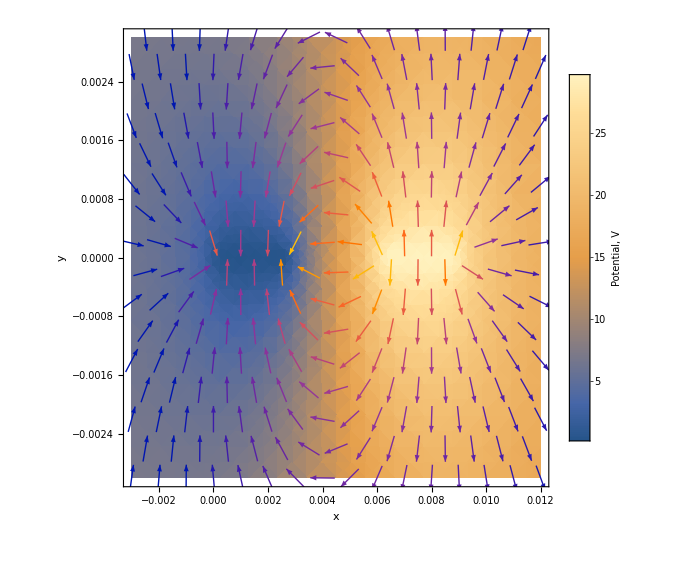

```mathematica
Show[DensityPlot[phiFun[x,y],{x,gridBoundLeft,gridBoundRight},{y,gridBoundDown,gridBoundUp},ImageSize->Large,PlotLegends->BarLegend[Automatic,LegendLabel->"Potential, V"],AxesLabel->{"x","y"}],VectorPlot[-field[x,y],{x,gridBoundLeft,gridBoundRight},{y,gridBoundDown,gridBoundUp},PlotLegends->BarLegend[Automatic,LegendLabel->"Electric field, V/m"],AxesLabel->{"x","y"}]]
```